```mathematica
a=0.066*0.1319T;
b=2.1*10^(-5)+2.6*10^(-18)*T;
c=0.063*0.1319T;
k=0.6931/23796;
(*T=94261147.2560784*250000/5*)
a/b -c/(b-k)Exp[-k*t]+(c*b-a(b-k))/(b(b-k))Exp[-b *t]
Simplify[a/b -c/(b-k)Exp[-k*t]+(c*b-a(b-k))/(b(b-k))Exp[-b *t]]
```

-(0.0083097 ⅇ^(-0.0000291267 t) T)/(-8.12674×10^-6+2.6×10^-18 T)+(0.0087054 T)/(0.000021+2.6×10^-18 T)+(ⅇ^(t (-0.000021-2.6×10^-18 T)) (-0.0087054 (-8.12674×10^-6+2.6×10^-18 T) T+0.0083097 (0.000021+2.6×10^-18 T) T))/((-8.12674×10^-6+2.6×10^-18 T) (0.000021+2.6×10^-18 T))

(ⅇ^(-0.0000291267 t) (-1.74504×10^-7+ⅇ^(t (8.12674×10^-6-2.6×10^-18 T)) (2.4525×10^-7-1.02882×10^-21 T)+ⅇ^(0.0000291267 t) (-7.07466×10^-8+2.2634×10^-20 T)-2.16052×10^-20 T) T)/(-1.70662×10^-10+3.34705×10^-23 T+6.76×10^-36 T^2)

Plot::pllim: Range specification {t} is not of the form {x, xmin, xmax}.

1.23381×10^15+8.25544×10^15 ⅇ^(-0.0000332539 x)-9.48925×10^15 ⅇ^(-0.0000291267 x)

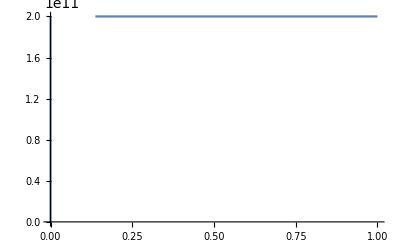

```mathematica
y=a/b-(c Exp[-k x])/(b-k)+((c b-a (b-k)) Exp[-b x])/(b (b-k))
Plot[y,{x,0,10000000},PlotRange->{0,2*10^11}]
```

```mathematica
1.2338098368214972*^15+8.255442894421377*^15 ⅇ^(-0.000033253949143290196 x)-8.25544×10^15 ⅇ^(-0.000029126743990586656 x)
```

-Graphics-

```mathematica
t=10000000; T=4713057362803.92;
y=(ⅇ^(-0.00002873548922056385 t) (-1.745037*^-7+ⅇ^(t (7.735489220563846*^-6-2.6000000000000004*^-18 T)) (2.418442278606965*^-7-1.0288200000000021*^-21 T)+ⅇ^(0.00002873548922056385 t) (-6.734052786069651*^-8+2.2634040000000005*^-20 T)-2.1605220000000003*^-20 T) T)/(-1.624452736318408*^-10+3.448772802653401*^-23 T+6.760000000000002*^-36 T^2)
```

1.23381×10^15